```mathematica
Seminarska naloga:
Bančne obresti
Avtor: Vito Štrucl
```

## Malo o zgodovini..

V 17 stoletju so trgovci svoje zlato začeli skladiščiti pri londonskih zlatarjih, ki so imeli zasebne trezorje, in za to storitev zaračunali taxo. V zameno za vsak depozit zlata so zlatarji izdali potrdila, ki potrjujejo količino in čistost kovine, ki so jo hranili kot varščina; teh potrdil ni bilo mogoče dodeliti, skladiščeno blago je lahko prevzel le originalni depozitar. Postopoma so zlatarji začeli posojati denar v imenu vlagateljev, kar je privedlo do razvoja sodobnih bančnih praks; zadolžnice (ki so se razvile v bankovce) so bile izdane za denar, deponiran kot posojilo zlatarju. Na osnovi teh vlog je zlatar plačeval obresti. Ker so se menice izplačale na zahtevo in so bili predujmi (posojila) strankam zlatarja vračljivi v daljšem časovnem obdobju, je bila to zgodnja oblika delnega rezervnega bančništva. Položnice so se razvile v ustrezen instrument, ki bi lahko krožil kot varna in priročna oblika denarja, podprta z obljubo zlatarja o plačilu, ki zlatarjem omogoča dajanje posojil z majhnim tveganjem neplačila. Tako so londonski zlatarji postali predhodniki bančništva z ustvarjanjem novega denarja na podlagi kreditov.

## Razumevanja obresti s pomočjo geometrijskega zaporedja.

Geometríjsko zaporedje je zaporedje števil, v katerem je neničelno število ( količnik dveh zaporednih členov) vedno  konstanten. Ta količnik se po navadi označi s črko k (količnik) ali mednarodno q (kvocient).
Členi zaporedja a1, a2, a3,...,an:
a1 = a1
a2 = a1*k
a3 = a2*k = a1*k^2

```mathematica
(*Na sploh bančne obresti delujejo kot splošno geometrijsko zaporedje*)


faktorobrestovanja = 1.01
glavnica = 10
glavnica2 = glavnica*faktorobrestovanja
glavnica3 = glavnica2 * faktorobrestovanja
```

1.01

10

10.1

## Kaj so Obresti?

Na splošno :
Obresti so finačni dolg, ki nastane ob posoijlu Denarja od trejte osebe oz. banke. Ko si sposodiš denar moraš plačati finančne obresti. Ko nekomu posodiš denar so oni tebi dolžni plačati obresti.Obstajajo številni načini kako izračunati obresti nekateri so za posojevalca bolj prikupni.To da se posameznik odloči odplačevati takšen dolg je odvisen od tega kaj bo ta storil/kupil s sposojenimi denarnimi sredstvi. Odločitev da boš posojeval denarna sredstva v zameno za obresti so odvisna od tega kaj drugega bi lahko počel s denarjem. 
 
Kaj so obresti :
Obresti se izračuna kot manjši (relativno na celoto) procent nekega posojila (ali depozita) ki se periodično izplača posojevalcem za privilegij uporabe njihovih denarnih sredstev. Ponavadi gre periodo enega leta, lahko je pa gre tudi za čas več ali manj kot eno leto (npr.Polletno, mesečno, tedensko, dnevno ..).

```mathematica
(*če zaračunmao faktor obrestovanja 1.01 na leto, poleta, mesec, teden, dan*)
glavnica1 = 1000
faktorobrestovanja1 = 1.01
izračun[čas_] = glavnica1*faktorobrestovanja1^(čas-1)
```

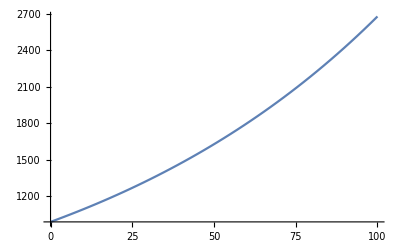

```mathematica
Plot[izračun[čas],{čas,0,100},PlotTheme->Automatic]
```

Pri tem je seveda vredno omeniti da obresti so dodaten dolg, ki sproti nastaja, ko si sposodimo denarna sredstva za dlje časa.Ko se posameznik oz.Firma namerava rešiti dolgov mora posojevalcu plačati nazaj isto vsoto kot si je sposodil in dogovorjeno obrestno mero ki je v času posojila nastala.

Ko sprejmeš posojilo : 
se zavezuješ, da boš vrnil osnovno vsoto ki si si jo sposodil.Ob tem moraš odplačevati odškodnino tvojemu posojevalcu (ki, s tem ko ti posoja svoja sredstva, izgubi dostop do njih) tako, da plačaš več kot si na začetku si sposodil.

Ko daješ posojilo : 
Če imaš lastne prihranke, jih sam lahko daš nekomu kot posojilo ali pa odpreš varčevalni račun v banki (s tem jim dovoljuješ da ta sredstva posojajo naprej ali pa investirajo v kar želijo).V zameno boš od njih pričakoval obresti, saj ti nimaš nobene koristi od tega da samo oddajaš sredstva. Višina obresti je odvisna od :

  • obrestne mere
  • višine posojila	
  • čas ki si ga je posameznik vzel, da je poplačal nastali dolg
  
  Višji kot je kateri koli od zgornjih treh faktorjev,višji je dolg ki ga je treba poravnati.

  *Večina bank in izdajateljev kreditnih kartic ne uporablja preprostih obresti.Namesto tega so obrestne spojine,kar ima za posledico zneske obresti,ki hitreje rastejo (glej spodaj).*

```mathematica
Manipulate[Plot[glavnica*obrestnamera^(čas-1),{čas, 0,100},  PlotRange->{{0,100},{0,100}}],{glavnica,0,10},{obrestnamera,1,2}]
```

Obrestna mera v 5 % na leto in stanje 100 evrov povzroči obresti v višini 5 evrov na leto, ob predpostavki, da uporabljate preproste obresti. Če spremenimo tri zgoraj navedene dejavnike in si lahko gledamo kako obrestna mera raste/pada. 

Pridobivanja zaslužka :  
Zaslužite, ko posojate denar ali nakažete sredstva na obrestni bančni račun, na primer varčevalni račun ali potrdilo o vlogi (CD).Banke posojajo za vas : vaš denar porabijo za posojilo drugim strankam in druge naložbe, del tega prihodka pa vam prenesejo v obliki obresti. Periodično (na primer vsak mesec ali četrtletje) banka na vaše prihranke plačuje obresti. Videli boste transakcijo za plačilo obresti in opazili boste, da se stanje na računu poveča. Ta denar lahko porabite ali ga hranite na računu, tako da bo še naprej zaslužil obresti. Vaši prihranki lahko resnično dobijo zagon, ko pustite zanimanje za svoj račun - zaslužili boste obresti na svojem prvotnem depozitu in tudi obresti, dodane v račun. Zaslužki na vrhu obresti, ki ste ga zaslužili prej, so znani kot sestavne obresti. 

Primer : Na varčevalni račun, ki plača 5 % obrestne mere, nakažete 1.000 EUR. S preprostimi obrestnimi merami bi v enem letu zaslužili 50 EUR.To izračunamo tako da 1.000 evrov prihranka prištejemo s 5 % od 1.000.

```mathematica
f[depozit_]:= depozit EUR * 1.0512 
f[1000]
```

1051.2 EUR

Plačevanje obresti :
Ko si izposodite denar, morate na splošno plačati obresti.To pa morda ni očitno - ni vedno transakcij z vrstico ali ločenega računa za stroške obresti.Obrok za obrok : Pri posojilih, kot so običajna posojila za stanovanje, avto in študente, se stroški obresti zaračunajo v mesečno plačilo.Vsak mesec del vašega plačila gre za zmanjšanje dolga, drugi del pa so stroški obresti.S temi posojili odplačate svoj dolg v določenem časovnem obdobju (na primer 15 - letna hipoteka ali 5 - letno posojilo za avtomobile).

Obnovljivi dolg :
Druga posojila so obnavljajoča se posojila, kar pomeni, da se lahko izposojate vsak mesec za mesecem in redno plačujete po dolgu.Na primer, kreditne kartice vam omogočajo, da večkrat porabite, dokler ostanete pod kreditnim limitom.Izračuni obresti se razlikujejo, vendar ni težko ugotoviti, kako se obračunajo obresti in kako delujejo vaša plačila.Dodatni stroški : Posojila se pogosto kotirajo z letno odstotno stopnjo (APR).Ta številka vam pove, koliko plačate na leto in lahko vključuje dodatne stroške nad in nad stroški obresti.Vaš čisti strošek obresti je “obrestna mera” (ne APR).Z nekaterimi posojili plačate stroške zapiranja ali stroške financiranja, ki tehnično niso stroški obresti, ki izvirajo iz zneska vašega posojila in vaše obrestne mere.Koristno bi bilo ugotoviti razliko med obrestno mero in APR.Za primerjavo je APR običajno boljše orodje.

```mathematica
Viri : -https : // simple.wikipedia.org/wiki/Bank #Banking _activities
-https : // ucilnica.fmf.uni - lj.si/pluginfile.php/44922/mod_resource/content/6/geomZaporedje.pdf
-https : // sl.wikipedia.org/wiki/Obresti
-https : // en.wikipedia.org/wiki/Interest
-https : // www.thebalance.com/what - is - interest - 315436
-https : // en.wikipedia.org/wiki/Bank #History
```